```mathematica
f[x_]:=FullSimplify[Max[Abs[Sin[x]],Abs[Cos[x]]],{Assumptions->Element[x,Reals]}]
```

```mathematica
f[x]
```

Max[Abs[Cos[x]],Abs[Sin[x]]]

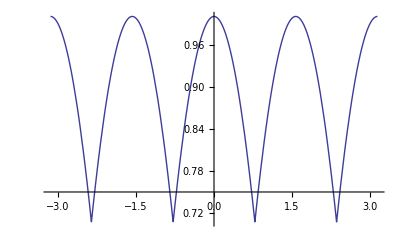

```mathematica
Plot[f[x],{x,-Pi,Pi}]
```

```mathematica
D[f[x],x]
```

Piecewise[{{-Sin[x] Abs'[Cos[x]], Abs[Cos[x]]-Abs[Sin[x]]≥0}, {Cos[x] Abs'[Sin[x]], True}}]

```mathematica
df[x_]=FullSimplify[D[f[x],x],{Assumptions->Element[x,Reals]}]
```

Piecewise[{{-Sign[Cos[x]] Sin[x], Abs[Cos[x]]≥Abs[Sin[x]]}, {Cos[x] Sign[Sin[x]], True}}]

```mathematica
df[x]
```

Piecewise[{{-Sign[Cos[x]] Sin[x], Abs[Cos[x]]≥Abs[Sin[x]]}, {Cos[x] Sign[Sin[x]], True}}]

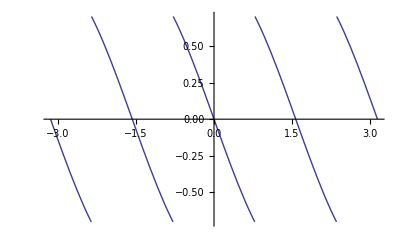

```mathematica
Plot[df[x],{x,-Pi,Pi}]
```

```mathematica
a0={{1,0,0},{0,1,0},{0,0,1}}
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
MatrixForm[a0]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
rr1[t1_]:={{Cos[t1],-Sin[t1],0},{Sin[t1],Cos[t1],0},{0,0,1}}
```

```mathematica
MatrixForm[rr1[t1]]
```

(Cos[t1] | -Sin[t1] | 0
Sin[t1] | Cos[t1] | 0
0 | 0 | 1)

```mathematica
a1=a0.rr1[t1]
```

{{Cos[t1],-Sin[t1],0},{Sin[t1],Cos[t1],0},{0,0,1}}

```mathematica
MatrixForm[a1]
```

(Cos[t1] | -Sin[t1] | 0
Sin[t1] | Cos[t1] | 0
0 | 0 | 1)

```mathematica
rr2[t2_]:={{1,0,0},{0,Cos[t2],-Sin[t2]},{0,Sin[t2],Cos[t2]}}
```

```mathematica
MatrixForm[rr2[t2]]
```

(1 | 0 | 0
0 | Cos[t2] | -Sin[t2]
0 | Sin[t2] | Cos[t2])

```mathematica
a2=a1.rr2[t2]
```

{{Cos[t1],-Cos[t2] Sin[t1],Sin[t1] Sin[t2]},{Sin[t1],Cos[t1] Cos[t2],-Cos[t1] Sin[t2]},{0,Sin[t2],Cos[t2]}}

```mathematica
MatrixForm[a2]
```

(Cos[t1] | -Cos[t2] Sin[t1] | Sin[t1] Sin[t2]
Sin[t1] | Cos[t1] Cos[t2] | -Cos[t1] Sin[t2]
0 | Sin[t2] | Cos[t2])

```mathematica
rr3[t3_]:={{Cos[t3],0,Sin[t3]},{0,1,0},{-Sin[t3],0,Cos[t3]}}
```

```mathematica
MatrixForm[rr3[t3]]
```

(Cos[t3] | 0 | Sin[t3]
0 | 1 | 0
-Sin[t3] | 0 | Cos[t3])

```mathematica
a3=a2.rr3[t3]
```

{{Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3],-Cos[t2] Sin[t1],Cos[t3] Sin[t1] Sin[t2]+Cos[t1] Sin[t3]},{Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3],Cos[t1] Cos[t2],-Cos[t1] Cos[t3] Sin[t2]+Sin[t1] Sin[t3]},{-Cos[t2] Sin[t3],Sin[t2],Cos[t2] Cos[t3]}}

```mathematica
MatrixForm[a3]
```

(Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3] | -Cos[t2] Sin[t1] | Cos[t3] Sin[t1] Sin[t2]+Cos[t1] Sin[t3]
Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3] | Cos[t1] Cos[t2] | -Cos[t1] Cos[t3] Sin[t2]+Sin[t1] Sin[t3]
-Cos[t2] Sin[t3] | Sin[t2] | Cos[t2] Cos[t3])

```mathematica
cur={{0.7080097953678469,0.23540010945942547,0.6658144772604981},{-0.7062020349687405,0.23720789540237627,0.6670915230796938},{0.0009030333269812496,0.9425068715002909,-0.3341855498155846}}
```

{{0.70801,0.2354,0.665814},{-0.706202,0.237208,0.667092},{0.000903033,0.942507,-0.334186}}

```mathematica
MatrixForm[cur]
```

(0.70801 | 0.2354 | 0.665814
-0.706202 | 0.237208 | 0.667092
0.000903033 | 0.942507 | -0.334186)

```mathematica
cur.Transpose[cur]
```

{{1.,1.66533×10^-16,-1.66533×10^-16},{1.66533×10^-16,1.,-8.32667×10^-17},{-1.66533×10^-16,-8.32667×10^-17,1.}}

```mathematica
pcur=cur.a3
```

{{-0.665814 Cos[t2] Sin[t3]+0.2354 (Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3])+0.70801 (Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3]),0.2354 Cos[t1] Cos[t2]-0.70801 Cos[t2] Sin[t1]+0.665814 Sin[t2],0.665814 Cos[t2] Cos[t3]+0.70801 (Cos[t3] Sin[t1] Sin[t2]+Cos[t1] Sin[t3])+0.2354 (-Cos[t1] Cos[t3] Sin[t2]+Sin[t1] Sin[t3])},{-0.667092 Cos[t2] Sin[t3]+0.237208 (Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3])-0.706202 (Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3]),0.237208 Cos[t1] Cos[t2]+0.706202 Cos[t2] Sin[t1]+0.667092 Sin[t2],0.667092 Cos[t2] Cos[t3]-0.706202 (Cos[t3] Sin[t1] Sin[t2]+Cos[t1] Sin[t3])+0.237208 (-Cos[t1] Cos[t3] Sin[t2]+Sin[t1] Sin[t3])},{0.334186 Cos[t2] Sin[t3]+0.942507 (Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3])+0.000903033 (Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3]),0.942507 Cos[t1] Cos[t2]-0.000903033 Cos[t2] Sin[t1]-0.334186 Sin[t2],-0.334186 Cos[t2] Cos[t3]+0.000903033 (Cos[t3] Sin[t1] Sin[t2]+Cos[t1] Sin[t3])+0.942507 (-Cos[t1] Cos[t3] Sin[t2]+Sin[t1] Sin[t3])}}

```mathematica
MatrixForm[pcur]
```

(-0.665814 Cos[t2] Sin[t3]+0.2354 (Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3])+0.70801 (Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3]) | 0.2354 Cos[t1] Cos[t2]-0.70801 Cos[t2] Sin[t1]+0.665814 Sin[t2] | 0.665814 Cos[t2] Cos[t3]+0.70801 (Cos[t3] Sin[t1] Sin[t2]+Cos[t1] Sin[t3])+0.2354 (-Cos[t1] Cos[t3] Sin[t2]+Sin[t1] Sin[t3])
-0.667092 Cos[t2] Sin[t3]+0.237208 (Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3])-0.706202 (Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3]) | 0.237208 Cos[t1] Cos[t2]+0.706202 Cos[t2] Sin[t1]+0.667092 Sin[t2] | 0.667092 Cos[t2] Cos[t3]-0.706202 (Cos[t3] Sin[t1] Sin[t2]+Cos[t1] Sin[t3])+0.237208 (-Cos[t1] Cos[t3] Sin[t2]+Sin[t1] Sin[t3])
0.334186 Cos[t2] Sin[t3]+0.942507 (Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3])+0.000903033 (Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3]) | 0.942507 Cos[t1] Cos[t2]-0.000903033 Cos[t2] Sin[t1]-0.334186 Sin[t2] | -0.334186 Cos[t2] Cos[t3]+0.000903033 (Cos[t3] Sin[t1] Sin[t2]+Cos[t1] Sin[t3])+0.942507 (-Cos[t1] Cos[t3] Sin[t2]+Sin[t1] Sin[t3]))

```mathematica
f1=Abs[pcur[[1,1]]]+Abs[pcur[[1,2]]]
```

Abs[0.2354 Cos[t1] Cos[t2]-0.70801 Cos[t2] Sin[t1]+0.665814 Sin[t2]]+Abs[-0.665814 Cos[t2] Sin[t3]+0.2354 (Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3])+0.70801 (Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3])]

```mathematica
f2=Abs[pcur[[2,1]]]+Abs[pcur[[2,2]]]
```

Abs[0.237208 Cos[t1] Cos[t2]+0.706202 Cos[t2] Sin[t1]+0.667092 Sin[t2]]+Abs[-0.667092 Cos[t2] Sin[t3]+0.237208 (Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3])-0.706202 (Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3])]

```mathematica
f3=Abs[pcur[[3,1]]]+Abs[pcur[[3,2]]]
```

Abs[0.942507 Cos[t1] Cos[t2]-0.000903033 Cos[t2] Sin[t1]-0.334186 Sin[t2]]+Abs[0.334186 Cos[t2] Sin[t3]+0.942507 (Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3])+0.000903033 (Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3])]

```mathematica
fmax=Max[f1,f2,f3]
```

Max[Abs[0.237208 Cos[t1] Cos[t2]+0.706202 Cos[t2] Sin[t1]+0.667092 Sin[t2]]+Abs[-0.667092 Cos[t2] Sin[t3]+0.237208 (Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3])-0.706202 (Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3])],Abs[0.942507 Cos[t1] Cos[t2]-0.000903033 Cos[t2] Sin[t1]-0.334186 Sin[t2]]+Abs[0.334186 Cos[t2] Sin[t3]+0.942507 (Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3])+0.000903033 (Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3])],Abs[0.2354 Cos[t1] Cos[t2]-0.70801 Cos[t2] Sin[t1]+0.665814 Sin[t2]]+Abs[-0.665814 Cos[t2] Sin[t3]+0.2354 (Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3])+0.70801 (Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3])]]

```mathematica
Simplify[fmax,Assumptions->{Element[t1,Reals],Element[t2,Reals],Element[t3,Reals]}]
```

Max[Abs[0.2354 Cos[t1] Cos[t2]-0.70801 Cos[t2] Sin[t1]+0.665814 Sin[t2]]+Abs[0.2354 Cos[t3] Sin[t1]-0.665814 Cos[t2] Sin[t3]-0.70801 Sin[t1] Sin[t2] Sin[t3]+Cos[t1] (0.70801 Cos[t3]+0.2354 Sin[t2] Sin[t3])],Abs[0.237208 Cos[t1] Cos[t2]+0.706202 Cos[t2] Sin[t1]+0.667092 Sin[t2]]+Abs[0.237208 Cos[t3] Sin[t1]-0.667092 Cos[t2] Sin[t3]+0.706202 Sin[t1] Sin[t2] Sin[t3]+Cos[t1] (-0.706202 Cos[t3]+0.237208 Sin[t2] Sin[t3])],Abs[0.942507 Cos[t1] Cos[t2]-0.000903033 Cos[t2] Sin[t1]-0.334186 Sin[t2]]+Abs[0.942507 Cos[t3] Sin[t1]+0.334186 Cos[t2] Sin[t3]-0.000903033 Sin[t1] Sin[t2] Sin[t3]+Cos[t1] (0.000903033 Cos[t3]+0.942507 Sin[t2] Sin[t3])]]

```mathematica
Simplify[fmax/.{t2->0,t3->0},Assumptions->{Element[t1,Reals]}]
```

Max[Abs[0.2354 Cos[t1]-0.70801 Sin[t1]]+Abs[0.70801 Cos[t1]+0.2354 Sin[t1]],Abs[0.706202 Cos[t1]-0.237208 Sin[t1]]+Abs[0.237208 Cos[t1]+0.706202 Sin[t1]],Abs[0.942507 Cos[t1]-0.000903033 Sin[t1]]+Abs[0.000903033 Cos[t1]+0.942507 Sin[t1]]]

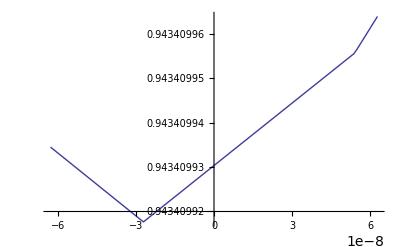

```mathematica
Plot[fmax/.{t2->0,t3->0},{t1,-Pi/50000000,Pi/50000000}]
```

```mathematica
Simplify[fmax/.{t1->0,t3->0},Assumptions->{Element[t2,Reals]}]
```

Max[0.000903033+Abs[0.942507 Cos[t2]-0.334186 Sin[t2]],0.70801+Abs[0.2354 Cos[t2]+0.665814 Sin[t2]],0.706202+Abs[0.237208 Cos[t2]+0.667092 Sin[t2]]]

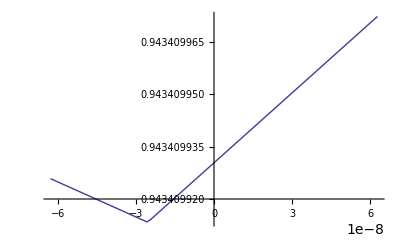

```mathematica
Plot[fmax/.{t1->0,t3->0},{t2,-Pi/50000000,Pi/50000000}]
```

```mathematica
Simplify[fmax/.{t1->0,t2->0},Assumptions->{Element[t3,Reals]}]
```

Max[0.2354+Abs[0.70801 Cos[t3]-0.665814 Sin[t3]],0.942507+Abs[0.000903033 Cos[t3]+0.334186 Sin[t3]],0.237208+Abs[0.706202 Cos[t3]+0.667092 Sin[t3]]]

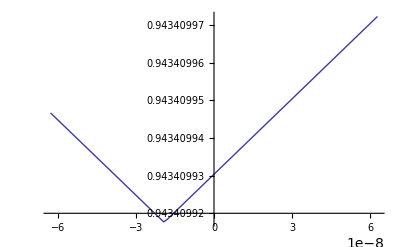

```mathematica
Plot[fmax/.{t1->0,t2->0},{t3,-Pi/50000000,Pi/50000000}]
```

```mathematica
dfmaxt1=Simplify[D[fmax/.{t2->0,t3->0},t1],Assumptions->{Element[t1,Reals]}]/.{Abs'->Sign}
```

Piecewise[{{Sign[0.70801 Cos[t1]+0.2354 Sin[t1]] (0.2354 Cos[t1]-0.70801 Sin[t1])+Sign[0.2354 Cos[t1]-0.70801 Sin[t1]] (-0.70801 Cos[t1]-0.2354 Sin[t1]), Abs[0.2354 Cos[t1]-0.70801 Sin[t1]]+Abs[0.70801 Cos[t1]+0.2354 Sin[t1]]≥Abs[0.706202 Cos[t1]-0.237208 Sin[t1]]+Abs[0.237208 Cos[t1]+0.706202 Sin[t1]]&&Abs[0.2354 Cos[t1]-0.70801 Sin[t1]]+Abs[0.70801 Cos[t1]+0.2354 Sin[t1]]≥Abs[0.942507 Cos[t1]-0.000903033 Sin[t1]]+Abs[0.000903033 Cos[t1]+0.942507 Sin[t1]]}, {Sign[0.237208 Cos[t1]+0.706202 Sin[t1]] (0.706202 Cos[t1]-0.237208 Sin[t1])+Sign[-0.706202 Cos[t1]+0.237208 Sin[t1]] (0.237208 Cos[t1]+0.706202 Sin[t1]), Abs[0.2354 Cos[t1]-0.70801 Sin[t1]]+Abs[0.70801 Cos[t1]+0.2354 Sin[t1]]<Abs[0.706202 Cos[t1]-0.237208 Sin[t1]]+Abs[0.237208 Cos[t1]+0.706202 Sin[t1]]&&Abs[0.942507 Cos[t1]-0.000903033 Sin[t1]]+Abs[0.000903033 Cos[t1]+0.942507 Sin[t1]]≤Abs[0.706202 Cos[t1]-0.237208 Sin[t1]]+Abs[0.237208 Cos[t1]+0.706202 Sin[t1]]}, {Sign[0.942507 Cos[t1]-0.000903033 Sin[t1]] (-0.000903033 Cos[t1]-0.942507 Sin[t1])+Sign[0.000903033 Cos[t1]+0.942507 Sin[t1]] (0.942507 Cos[t1]-0.000903033 Sin[t1]), True}}]

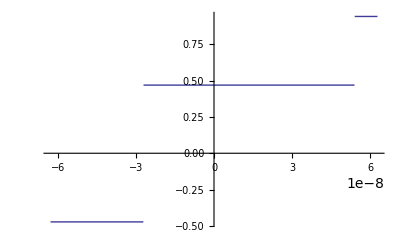

```mathematica
Plot[dfmaxt1,{t1,-Pi/50000000,Pi/50000000}]
```

```mathematica
dfmaxt2=Simplify[D[fmax/.{t1->0,t3->0},t2],Assumptions->{Element[t2,Reals]}]/.{Abs'->Sign}
```

Piecewise[{{Sign[0.942507 Cos[t2]-0.334186 Sin[t2]] (-0.334186 Cos[t2]-0.942507 Sin[t2]), Abs[0.942507 Cos[t2]-0.334186 Sin[t2]]≥0.707107+Abs[0.2354 Cos[t2]+0.665814 Sin[t2]]&&Abs[0.942507 Cos[t2]-0.334186 Sin[t2]]≥0.705299+Abs[0.237208 Cos[t2]+0.667092 Sin[t2]]}, {Sign[0.2354 Cos[t2]+0.665814 Sin[t2]] (0.665814 Cos[t2]-0.2354 Sin[t2]), Abs[0.942507 Cos[t2]-0.334186 Sin[t2]]<0.707107+Abs[0.2354 Cos[t2]+0.665814 Sin[t2]]&&0.00180776+Abs[0.2354 Cos[t2]+0.665814 Sin[t2]]≥Abs[0.237208 Cos[t2]+0.667092 Sin[t2]]}, {Sign[0.237208 Cos[t2]+0.667092 Sin[t2]] (0.667092 Cos[t2]-0.237208 Sin[t2]), True}}]

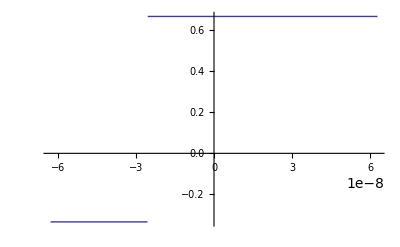

```mathematica
Plot[dfmaxt2,{t2,-Pi/50000000,Pi/50000000}]
```

```mathematica
dfmaxt3=Simplify[D[fmax/.{t1->0,t2->0},t3],Assumptions->{Element[t3,Reals]}]/.{Abs'->Sign}
```

Piecewise[{{Sign[-0.706202 Cos[t3]-0.667092 Sin[t3]] (-0.667092 Cos[t3]+0.706202 Sin[t3]), 0.00180779+Abs[0.706202 Cos[t3]+0.667092 Sin[t3]]≥Abs[0.70801 Cos[t3]-0.665814 Sin[t3]]&&Abs[0.706202 Cos[t3]+0.667092 Sin[t3]]≥0.705299+Abs[0.000903033 Cos[t3]+0.334186 Sin[t3]]}, {Sign[0.70801 Cos[t3]-0.665814 Sin[t3]] (-0.665814 Cos[t3]-0.70801 Sin[t3]), 0.00180779+Abs[0.706202 Cos[t3]+0.667092 Sin[t3]]<Abs[0.70801 Cos[t3]-0.665814 Sin[t3]]&&Abs[0.70801 Cos[t3]-0.665814 Sin[t3]]≥0.707107+Abs[0.000903033 Cos[t3]+0.334186 Sin[t3]]}, {Sign[0.000903033 Cos[t3]+0.334186 Sin[t3]] (0.334186 Cos[t3]-0.000903033 Sin[t3]), True}}]

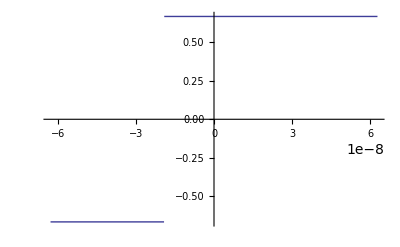

```mathematica
Plot[dfmaxt3,{t3,-Pi/50000000,Pi/50000000}]
```

```mathematica
dfmaxt1/.{t1->0}
```

0.468994

```mathematica
dfmaxt2/.{t2->0}
```

0.667092

```mathematica
dfmaxt3/.{t3->0}
```

0.667092

```mathematica
FindMinimum[fmax/.{t2->0,t3->0},{t1,0}]
```

{0.94341,{t1→-3.32152×10^-8}}

```mathematica
FindMinimum[fmax/.{t1->0,t3->0},{t2,0}]
```

{0.94341,{t2→-3.76153×10^-8}}

```mathematica
FindMinimum[fmax/.{t1->0,t2->0},{t3,0}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.94341,{t3→-2.31171×10^-8}}

```mathematica
minpcur=pcur/.{t1->-3.321522746265248*^-8,t2->-3.7615280774684614*^-8,t3->-2.3117141220268175*^-8}
```

{{0.70801,0.2354,0.665814},{-0.706202,0.237208,0.667092},{0.000902994,0.942507,-0.334186}}

```mathematica
MatrixForm[minpcur]
```

(0.70801 | 0.2354 | 0.665814
-0.706202 | 0.237208 | 0.667092
0.000902994 | 0.942507 | -0.334186)

```mathematica
MatrixForm[minpcur-cur]
```

(7.57286×10^-9 | -1.52809×10^-9 | -7.51252×10^-9
7.54234×10^-9 | -4.85495×10^-8 | 2.5248×10^-8
-3.9031×10^-8 | 1.26005×10^-8 | 3.54318×10^-8)

```mathematica
RotateRows[minpcur,1,2,{t->0}]
```

0.94341

0.94341

0.94341

(0.70801 | 0.2354 | 0.665814
-0.706202 | 0.237208 | 0.667092
0.000902994 | 0.942507 | -0.334186)

{{0.70801,0.2354,0.665814},{-0.706202,0.237208,0.667092},{0.000902994,0.942507,-0.334186}}

```mathematica
b={{Sqrt[2]/2,Sqrt[2]/6,2/3},
{-Sqrt[2]/2,Sqrt[2]/6,2/3},
{0,Sqrt[8/9],-1/3}};
```

```mathematica
MatrixForm[b]
```

(1/(√2) | 1/(3 √2) | 2/3
-1/(√2) | 1/(3 √2) | 2/3
0 | (2 √2)/3 | -1/3)

```mathematica
MatrixForm[b.Transpose[b]]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
pb=b.a3;
```

```mathematica
MatrixForm[pb]
```

(-2/3 Cos[t2] Sin[t3]+(Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3])/(3 √2)+(Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3])/(√2) | (Cos[t1] Cos[t2])/(3 √2)-(Cos[t2] Sin[t1])/(√2)+(2 Sin[t2])/3 | 2/3 Cos[t2] Cos[t3]+(Cos[t3] Sin[t1] Sin[t2]+Cos[t1] Sin[t3])/(√2)+(-Cos[t1] Cos[t3] Sin[t2]+Sin[t1] Sin[t3])/(3 √2)
-2/3 Cos[t2] Sin[t3]+(Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3])/(3 √2)-(Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3])/(√2) | (Cos[t1] Cos[t2])/(3 √2)+(Cos[t2] Sin[t1])/(√2)+(2 Sin[t2])/3 | 2/3 Cos[t2] Cos[t3]-(Cos[t3] Sin[t1] Sin[t2]+Cos[t1] Sin[t3])/(√2)+(-Cos[t1] Cos[t3] Sin[t2]+Sin[t1] Sin[t3])/(3 √2)
1/3 Cos[t2] Sin[t3]+2/3 √2 (Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3]) | 2/3 √2 Cos[t1] Cos[t2]-Sin[t2]/3 | -1/3 Cos[t2] Cos[t3]+2/3 √2 (-Cos[t1] Cos[t3] Sin[t2]+Sin[t1] Sin[t3]))

```mathematica
f1=Abs[pb[[1,1]]]+Abs[pb[[1,2]]]
```

Abs[(Cos[t1] Cos[t2])/(3 √2)-(Cos[t2] Sin[t1])/(√2)+(2 Sin[t2])/3]+Abs[-2/3 Cos[t2] Sin[t3]+(Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3])/(3 √2)+(Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3])/(√2)]

```mathematica
f2=Abs[pb[[2,1]]]+Abs[pb[[2,2]]]
```

Abs[(Cos[t1] Cos[t2])/(3 √2)+(Cos[t2] Sin[t1])/(√2)+(2 Sin[t2])/3]+Abs[-2/3 Cos[t2] Sin[t3]+(Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3])/(3 √2)-(Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3])/(√2)]

```mathematica
f3=Abs[pb[[3,1]]]+Abs[pb[[3,2]]]
```

Abs[2/3 √2 Cos[t1] Cos[t2]-Sin[t2]/3]+Abs[1/3 Cos[t2] Sin[t3]+2/3 √2 (Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3])]

```mathematica
fmax=Max[f1,f2,f3]
```

Max[Abs[2/3 √2 Cos[t1] Cos[t2]-Sin[t2]/3]+Abs[1/3 Cos[t2] Sin[t3]+2/3 √2 (Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3])],Abs[(Cos[t1] Cos[t2])/(3 √2)+(Cos[t2] Sin[t1])/(√2)+(2 Sin[t2])/3]+Abs[-2/3 Cos[t2] Sin[t3]+(Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3])/(3 √2)-(Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3])/(√2)],Abs[(Cos[t1] Cos[t2])/(3 √2)-(Cos[t2] Sin[t1])/(√2)+(2 Sin[t2])/3]+Abs[-2/3 Cos[t2] Sin[t3]+(Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3])/(3 √2)+(Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3])/(√2)]]

```mathematica
Simplify[fmax/.{t2->0,t3->0},Assumptions->{Element[t1,Reals]}]
```

2/3 √2 (Abs[Cos[t1]]+Abs[Sin[t1]])

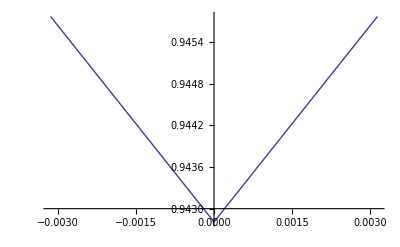

```mathematica
Plot[fmax/.{t2->0,t3->0},{t1,-Pi/1000,Pi/1000}]
```

```mathematica
Simplify[fmax/.{t1->0,t3->0},Assumptions->{Element[t2,Reals]}]
```

Max[1/3 Abs[2 √2 Cos[t2]-Sin[t2]],1/(√2)+1/6 Abs[√2 Cos[t2]+4 Sin[t2]]]

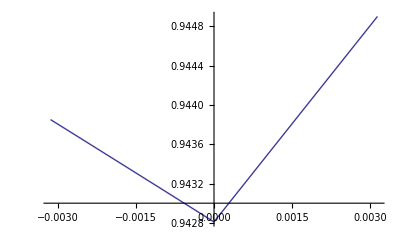

```mathematica
Plot[fmax/.{t1->0,t3->0},{t2,-Pi/1000,Pi/1000}]
```

```mathematica
Simplify[fmax/.{t1->0,t2->0},Assumptions->{Element[t3,Reals]}]
```

Max[1/6 (√2+Abs[3 √2 Cos[t3]-4 Sin[t3]]),1/3 (2 √2+Abs[Sin[t3]]),1/6 (√2+Abs[3 √2 Cos[t3]+4 Sin[t3]])]

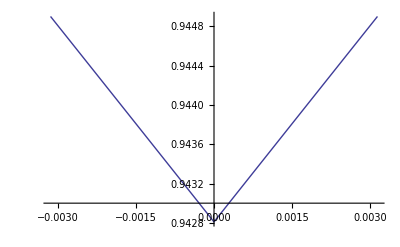

```mathematica
Plot[fmax/.{t1->0,t2->0},{t3,-Pi/1000,Pi/1000}]
```

```mathematica
Animate[Plot3D[fmax/.{t3->t},{t1,-Pi/1000,Pi/1000},{t2,-Pi/1000,Pi/1000},PlotPoints->{25,25},Mesh->None],{t,-Pi/1000,Pi/1000,Pi/20000},AnimationRunning->False,AnimationRate->0.2]
```

```mathematica
FindMinimum[fmax/.{t3->0},{{t1,1/1000},{t2,1/1000}},WorkingPrecision->40]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than 40. digits of working precision to meet these tolerances.

{0.9428092617679190988544212180181975749933,{t1→-1.173687230259584827483053059298438035972×10^-21,t2→-6.605581842728701350356996551544545279421×10^-7}}

```mathematica
N[Sqrt[8/9],40]
```

0.9428090415820633658677924828064653857131